# Problem Set 3.2

```mathematica
f[x_, y_, ε_, Iext_] := 1/ε * (x - 1/3*x^3 - y + Iext)
g[x_, y_, a_, b_] := x + a - b*y

J[x_, ε_] := ({{(1-x^2)/ε, -1/ε}, {1, -b}})
```

```mathematica
a = 4/9;
b = 5/9;
ε = 1;
```

```mathematica
xrange = 1;
yrange = 1;
Irange = 1;

Manipulate[
	Show[
		StreamPlot[{f[x,y,ε,Iext], g[x,y,a,b]}, {x, -xrange, xrange}, {y, -yrange, yrange},
		StreamStyle -> Automatic,
		StreamColorFunction -> "Rainbow",
		FrameLabel -> {"x", "y"},
		StreamPoints -> Fine,
		AspectRatio -> 1]
	],
{Iext,0,Irange}]
```

```mathematica
numPoints = 100;
Ivals = Subdivide[0, 1, numPoints];(*Table that contains a list of i values*);

ReLambda = Table[0.0, {numPoints + 1}];
ImLambda = Table[0.0, {numPoints + 1}];
fixedXs = Table[0.0, {numPoints + 1}];
fixedXprev = -0.8; (*From plot above*)

Do[
	Icurrent = Ivals[[j]];
	fixedX = x /. Quiet[
		FindRoot[
		    x - (1/3) * x^3 - (x + a)/b + Icurrent == 0, 
		    {x, fixedXprev}, 
		    Method -> "Newton", 
		    MaxIterations -> 100, 
		    AccuracyGoal -> 10
	    ]
	];
	(* Compute y from fixedX *)
	fixedY = (fixedX + a)/b;
  
	(* Update the previous x for the next iteration *)
	fixedXprev = fixedX;
	fixedXs[[j]] = fixedX;
  
	(* Compute the eigenvalues of the Jacobian *)
	eig = Eigenvalues[J[fixedX, ε]];
  
	(* Store the real and imaginary parts *)
	ReLambda[[j]] = Re[eig[[1]]];
	ImLambda[[j]] = Im[eig[[1]]];
  
	,
	{j, 1, numPoints + 1}
];
dataX = Transpose@{Ivals, fixedXs};
dataRe = Transpose@{Ivals, ReLambda}; (*Transform and combine the lists so that they contain points (i, Re[ev[i]])*)
dataIm = Transpose@{Ivals, ImLambda};
(*Plot the points (i, Re[eig]) and (i, Im[eig]) in the same plot. Don't forget to label the bifurcation point and add a legend to denote which points (or line if you use ListLinePlot) corresponds to the real part of the eigenvalue and which to the imaginary part.*)
```

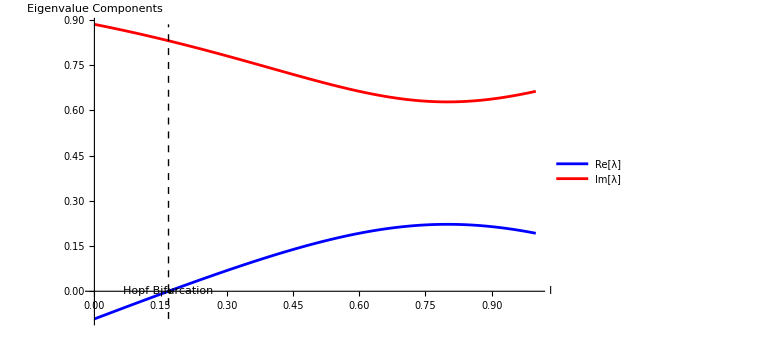

```mathematica
(*Plot the points (i, Re[eig]) and (i, Im[eig]) in the same plot. 
Don't forget to label the bifurcation point and add a legend 
to denote which points (or line if you use ListLinePlot) 
corresponds to the real part of the eigenvalue and which to the imaginary part.*)
Ihopf = 68/405;
ListLinePlot[
  {
    dataRe,
    dataIm  
  },
  PlotLegends -> {"Re[λ]", "Im[λ]"},
  AxesLabel -> {"I", "Eigenvalue Components"},
  PlotStyle -> {Blue, Red},
  PlotRange -> All,
  ImageSize -> Large,
  Epilog -> {
        {Black, Dashed, Line[{{Ihopf, Min[ReLambda, ImLambda]}, {Ihopf, Max[ReLambda, ImLambda]}}]},
        {Black, PointSize[Large], Point[{Ihopf, 0}]},
        Text["Hopf Bifurcation", {Ihopf, 0}, {1.2, 0}]
        }
]
```

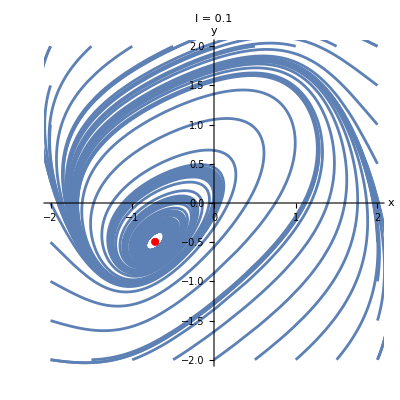

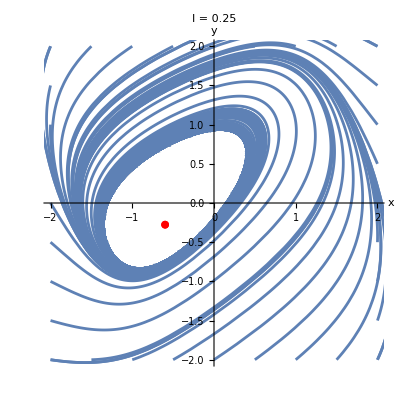

```mathematica
maxt = 50;
sol[x0_, y0_, Iext_] := NDSolve[{x'[t] == 1/ε * (x[t] - 1/3*x[t]^3 - y[t] + Iext), y'[t] == x[t] + a - b*y[t], x[0]==x0,y[0]==y0},
								{x,y},
								{t,0,maxt}]
minx=-2;
miny=-2;
maxx=2;
maxy=2;
step = 0.5;
initialC=Join[
			Table[{minx,y},{y,miny,maxy,step}],
			Table[{maxx,y},{y,miny,maxy,step}],
			Table[{x,miny},{x,minx,maxx,step}],
			Table[{x,maxy},{x,minx,maxx,step}]];
Iext = 0.1;
fixedX = -0.7196844116363366;
p1=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧, Iext]],
			{t,0,maxt},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ListPlot[{{fixedX, (fixedX + a)/b}}, 
		PlotStyle->{Red}, 
		PlotMarkers->{Automatic, 8}
	],
	PlotLabel -> "I = " <> ToString[Iext]
]

Iext = 0.25;
fixedX = -0.5982743232213728;
p1=Show[
	Table[
		ParametricPlot[
			Evaluate[{x[t],y[t]}/. sol[initialC⟦i,1⟧, initialC⟦i,2⟧, Iext]],
			{t,0,maxt},
			PlotRange->{{minx,maxx},{miny,maxy}},
			AxesLabel->{x,y}
		]
		/. Line[x_]:>{Arrowheads[{{0.05, 0.5}, {0.05, 0.0}}],Arrow[x]},{i,1,Length[initialC]}
	], 
	ListPlot[{{fixedX, (fixedX + a)/b}}, 
		PlotStyle->{Red}, 
		PlotMarkers->{Automatic, 8}
	],
	PlotLabel -> "I = " <> ToString[Iext]
]
```